```mathematica
(*s = Import["C:\\Users\\Wargass\\Desktop\\total_donations_ordered.csv"];
zip = s[[All,2]];
donations = s[[All,4]];
Histogram[zip](*This lets us see how many people are donating from specific reagions of the country. Because all of the zipcodes that start with zero are grouped together anyway they shouldn't be a concern during further analysis*)
Histogram[donations, PlotRange->Automatic]*)
```

```mathematica
m=SemanticImport["C:\\Users\\TEMP\\Desktop\\total_donations_ordered.csv", CharacterEncoding->"UTF8"];
```

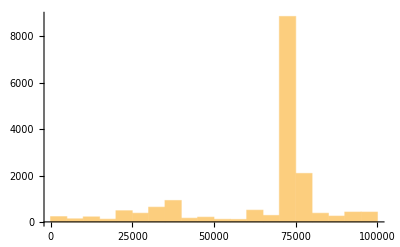

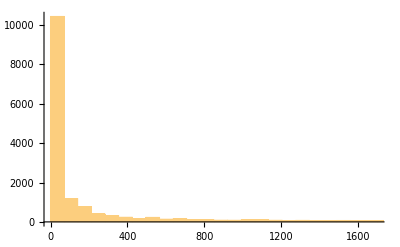

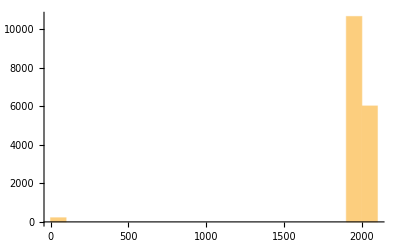

```mathematica
mID = Normal[m[[All,1]]];
mzip = Normal[m[[All,2]]];
mgrad = Normal[m[[All,3]]];
mdonation = Normal[m[[All,5]]];
Histogram[mzip]
Histogram[mdonation]
Histogram[mgrad]
```

```mathematica
zipcodes = Entity["ZIPCode"]/@ToString/@mzip
```

Syntax::sntxf: "Entity[ZIPCode]/@" cannot be followed by "[ToString/@mzip]".

```mathematica
GeoRegionValuePlot[Rule @@ Transpose[zipcodes],ImageSize->Medium, GeoRange->"Country"]
```

```mathematica
position = Interpreter["Location"]["Hendrix College"];
```

```mathematica
GeoGraphics[GeoMarker@position, ImageSize->Medium, GeoRange->"Country"]
```

-Graphics-

```mathematica
?SemanticImport
```

SemanticImport[file] attempts to import a file semantically to give a Dataset object.
SemanticImport[file,type] attempts to interpret all elements in the file as being of the specified type.
SemanticImport[file,{type_1,type_2,…}] attempts to interpret elements in successive columns as being of the specified types. 
SemanticImport[file,<|col_1->type_1,col_2->type_2,…|>] keeps only the columns col_i specified by their positions or names.
SemanticImport[file,typespec,form] puts the result in the specified form.